```mathematica
t
```

t

```mathematica
(*n = no+8*A* Cos[2*π*x]*Cos[2*π*y]*Cos[2*π*z] + 2*B*(Cos[4*π*x]+ Cos[4*π*y]+Cos[4*π*z]);
a = 1;
fideal = τ*(no + 1) * Log[((no+ 1)* (1 - b))/(1 - (no + 1) * b)] - a1* no^2;
Fid = (1/a)^3 *Integrate[fideal, {x, 0, a}, {y, 0, a}, {z, 0, a}];*)
Fideal = τ*(no + 1)* Log[(no + 1)*(1 - b)/(1 - (no+1)*b)] - a1*no^2 - τ/(1-b) * no;
Fcorr =  (- τ)/2* Bx* Exp[-τ/Tm]*( 8*A^2+6*B^2) ;
(*Fzeta= (1/a)^3 *Integrate[a2/2(n^2 - no*n)  + a3/3*(n^3 - no^2*n) + a4/4*(n^4-no^3*n), {x, 0, a}, {y, 0, a}, {z, 0, a}];*)Fzeta = 54 A^4 a4+3/2 B^2 (2 a2+15 a4 B^2+4 a3 no+6 a4 no^2)+4 A^2 (a2+2 a3 (3 B+no)+3 a4 (12 B^2+6 B no+no^2)) ;
Fk0 = 0.2*τ/2* no^2;
F = Fideal + Fcorr + Fzeta + Fk0;
```

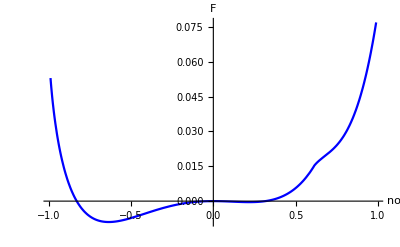

```mathematica
pVal =0.3;
kappaVal = 0.45;
mVal = 2;

a1Val = 0.5;
bVal = 0.4;

sVal= 1.0 + 0.75*τ;
tVal= 1.8 + 0.1* τ;
vVal = 0.8;

a2Val =(0.3 + kappa*(no-m)^2 )* τ+0.225* τ^2 ;
a3Val = -0.27* τ-0.015*τ^2;
a4Val = 0.08* τ;

BxVal = 1.0;
TmVal= 10;
dVal = 0.2;


nmin = -0.99;
nmax = 0.99;
nStep = 0.01;

Fsubs = F/.{a1-> a1Val, b->bVal, a2->a2Val, a3->a3Val, a4-> a4Val};
Fsubs = Fsubs/.{ Bx -> BxVal, Tm-> TmVal, d -> dVal, p -> pVal, kappa -> kappaVal, m -> mVal};
Ffcc[n0_, T_]:= FindMinimum[{Fsubs/.{ no->n0,τ -> T}, {A, B} ∈ Reals, A≥ 0, 0≤B<A}, {{A, 1.0}, {B, 1.0}}][[1]];
Fl[n0_, T_] := Fsubs/.{A -> 0, B-> 0, no->n0, τ -> T}; 
plottingT = 0.32;
Show[Plot[{Ffcc[nn, plottingT]}, {nn, nmin, nmax}, PlotStyle->{Blue}, AxesLabel->{"no", "F"}]]
```

```mathematica
BxVal * Exp[-0.32/TmVal]
```

0.968507

```mathematica
a3Val/.{τ -> plottingT}
```

-0.087936

```mathematica
a4Val/.{τ -> plottingT}
```

0.0256

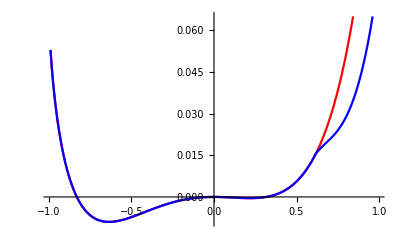

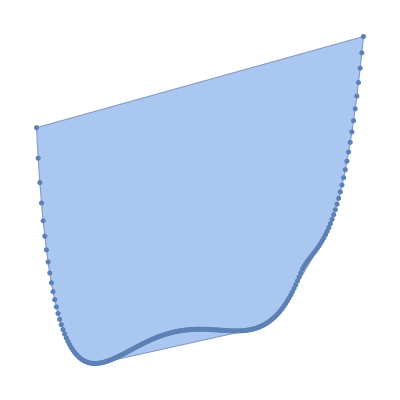

-Graphics3D-

-Graphics3D-

```mathematica
Show[Plot[{Fl[nn, plottingT],Ffcc[nn, plottingT]}, {nn, nmin, nmax}, PlotStyle->{Red, Blue}]]

fcn=Table[{i,Ffcc[i, plottingT]},{i,nmin,nmax,nStep}]  ;
convHull = ConvexHullMesh[fcn];
Show[convHull,ListPlot[fcn],AspectRatio->1]

G[n0_, T_] := FindMinimum[{Fsubs/.{no->n0, τ -> T}, {A, B} ∈ Reals, A≥ 0, 0≤B<A}, {{A, 1.0}, {B, 1.0}}][[2, 1]];
H[n0_, T_] := FindMinimum[{Fsubs/.{no->n0, τ -> T}, {A, B} ∈ Reals, A≥ 0, 0≤B<A}, {{A, 1.0}, {B, 1.0}}][[2, 2]];
Show[Plot3D[A/.G[nn, T], {nn, nmin, nmax}, {T, 0.25, 0.6}, AxesLabel->{"A", "no", "τ"}]]
Show[Plot3D[B/.H[nn, T], {nn, nmin, nmax}, {T, 0.25, 0.6},AxesLabel->{"B", "no", "τ"}]]
```

```mathematica
FmattPlotter[n0_, T_] := Fmatt/.{p -> pVal, kappa -> kappaVal, m -> mVal, Subscript[n, o]->n0, τ -> T, A-> G[n0, T], B-> H[n0, T]};
```

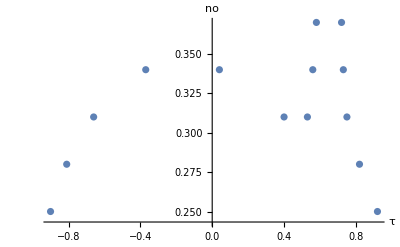

```mathematica
commonTangent = {};
convexStep = 0.01;
For[T= 0.25, T< 0.4, T = T + 0.03, 
	fcn=Table[{i,Ffcc[i, T]},{i,-0.99,1.4,convexStep}]  ;
	convHull = ConvexHullMesh[fcn];
	convHulln = MeshCoordinates[convHull][[All, 1]];

	len = Length[convHulln];
	dummy = {};

	For[i =  len, i>2, i--,
	If[Abs[convHulln[[i]] -(convHulln[[i - 1]] )]- convexStep>0.000001  ,
	dummy = Append[dummy, {convHulln[[i]], convHulln[[i - 1]]}]
	]
	];
	
	For[ j = 1, j <= Length[dummy], j++,
	commonTangent = Append[commonTangent, {dummy[[j,1]], T}];
	commonTangent = Append[commonTangent, {dummy[[j,2]], T}];
	];
];
ListPlot[commonTangent, AxesLabel->{"τ", "no"}]
```